Generate a set of x_i + Delta x (Δx)

```mathematica
Δx=0.001;α=16;Tol=10^-6;
SetGradGenPos={};
GradGenPos=InitialGeneratorPosition;
For[iI=1,iI≤Length[InitialGeneratorPosition],iI++,
For[jJ=1,jJ≤ 2,jJ++,
GradGenPos[[iI]][[jJ]]=InitialGeneratorPosition[[iI]][[jJ]]+Δx;
SetGradGenPos=Join[SetGradGenPos,{GradGenPos}];
GradGenPos=InitialGeneratorPosition
]
]
```

Compute Gradient

```mathematica
GradX={};
For[iI=1,iI<=2*Length[GradGenPos],iI++,
Gradd=(CCVTFunction[SetGradGenPos[[iI]]]-CCVTFunction[InitialGeneratorPosition])/Δx;
GradX=Join[GradX,{{Gradd}}]
];
DevOriginal=CCVTFunction[InitialGeneratorPosition];
Print["At Initial, the objective function value is ", CCVTFunction[InitialGeneratorPosition]," with gradient ∇X= ",MatrixForm[GradX]," with α=", α];

X={};XX={};
For[iI=1,iI≤ Length[InitialGeneratorPosition],iI++,
XX=Join[XX,InitialGeneratorPosition[[iI]]];
];
For[iI=1,iI≤Length[XX],iI++,
X=Join[X,{{XX[[iI]]}}];
]
```

At Initial, the objective function value is 0.241493 with gradient ∇X= (-0.82961
34.068
0.616277
0.926111
0.982447
-0.142401
0.619453
0.327158
1.66373
-0.126205
-0.568932
2.64838
1.32021
2.21151
0.571191
0.500365
0.723581
-0.283976
0.329268
-1.66212) with α=16

Iteration

Round 1, Dev is 0.241493 with α=16

Round 2, Dev is 0.241493 with α=8.

Round 3, Dev is 0.241493 with α=4.

Round 4, Dev is 0.241493 with α=2.

Round 5, Dev is 0.241493 with α=1.

Round 6, Dev is 0.241493 with α=0.5

Round 7, Dev is 0.241493 with α=0.25

Round 8, Dev is 0.0686716 with α=0.3125

Round 9, Dev is 0.0686716 with α=0.15625

Round 10, Dev is 0.0157639 with α=0.195313

Round 11, Dev is 0.0157639 with α=0.0976563

Round 12, Dev is 0.0157639 with α=0.0488281

Round 13, Dev is 0.0157639 with α=0.0244141

Round 14, Dev is 0.0157639 with α=0.012207

Round 15, Dev is 0.0157639 with α=0.00610352

Round 16, Dev is 0.014462 with α=0.00762939

Round 17, Dev is 0.014462 with α=0.0038147

Round 18, Dev is 0.0119798 with α=0.00476837

Round 19, Dev is 0.0119798 with α=0.00238419

Round 20, Dev is 0.0119798 with α=0.00119209

Round 21, Dev is 0.0115752 with α=0.00149012

Round 22, Dev is 0.0115752 with α=0.000745058

Round 23, Dev is 0.0115752 with α=0.000372529

Round 24, Dev is 0.0115752 with α=0.000186265

Round 25, Dev is 0.0115752 with α=0.0000931323

Round 26, Dev is 0.0115752 with α=0.0000465661

Round 27, Dev is 0.0115752 with α=0.0000232831

Round 28, Dev is 0.0115752 with α=0.0000116415

Round 29, Dev is 0.0115752 with α=5.82077×10^-6

Round 30, Dev is 0.0115752 with α=2.91038×10^-6

Round 31, Dev is 0.0115752 with α=1.45519×10^-6

{0.241493,0.0686716,0.0157639,0.014462,0.0119798}

{}

Number of function computation= 152

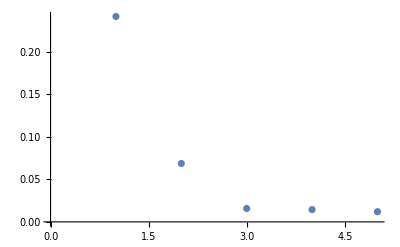

{{-0.246374,0.138534},{-0.444805,0.53868},{-0.399643,0.584955},{-0.501258,0.461091},{-0.45457,0.13258},{-0.265468,0.419469},{-0.232418,0.245473},{-0.444941,0.263077},{-0.0139689,0.108247},{-0.192717,0.301769}}

0.0115752

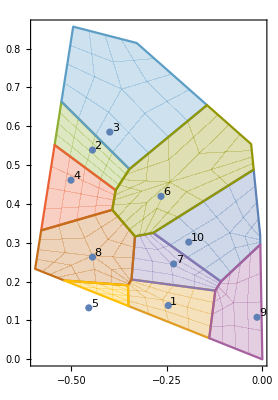

0.0115752

FunctionResult =0.0115752

AreaError =0.00439443

Penalty =2.76762×10^-6

PenaltyCompactness =4.75176×10^-6

PernaltyTopo =0.00717322

```mathematica
DevOriginalPlot={};DecPlot={};CountIt=1;CounterY=1;
(*Number = computation of value and approx gradients *)
FunctionCompCount=1+2*Length[InitialGeneratorPosition];
(*Initial Step*)
Y=X-α*GradX/Norm[GradX];
DevXOriginal=DevOriginal;
(*LOOOOOOP*)
While[α>Tol,
(*Generate set SolY for computing VD*)
(*Go Go Go*)
Y=X-α*GradX/Norm[GradX];
YY={};
For[iI=1,iI≤ Length[Y],iI++,
YY=Join[YY,Y[[iI]]]
];
SolY=Partition[YY,2];
(*Compute function*)
CCVTYValue=CCVTFunction[SolY];
Print[" Round ",CounterY,", Dev is ",DevXOriginal," with α=", α];
If[CCVTYValue<DevXOriginal,
DevOriginalPlot=Join[DevOriginalPlot,{DevXOriginal}];
X=Y;
SolX=SolY;
DevXOriginal=CCVTYValue;
(*New Gradient Computation*)
GradX={};
SetGradGenPos={};
GradGenPos=SolX;
For[iI=1,iI≤Length[SolX],iI++,
For[jJ=1,jJ≤ 2,jJ++,
GradGenPos[[iI]][[jJ]]=SolX[[iI]][[jJ]]+Δx;
SetGradGenPos=Join[SetGradGenPos,{GradGenPos}];
GradGenPos=SolX
]
];
For[iI=1,iI<=2*Length[GradGenPos],iI++,
Gradd=(CCVTFunction[SetGradGenPos[[iI]]]-DevXOriginal)/Δx;
GradX=Join[GradX,{{Gradd}}]
];
α=1.25*α;
CounterY=CounterY+1;
FunctionCompCount=FunctionCompCount+1+2*Length[InitialGeneratorPosition];
,(*Otherwise*)
α=0.5*α;
CounterY=CounterY+1;
FunctionCompCount=FunctionCompCount+1;
];

];
Print[DevOriginalPlot];
Print[DecPlot];
Print["Number of function computation= ", FunctionCompCount];
ListPlot[DevOriginalPlot]
Print[SolX]
CCVTFunction[SolX]
CCVTFunctionPlot[SolX]
CCVTFunction1[SolX]
```

```mathematica
d
```